## A Must Run

```mathematica
Off[Solve::svars]
```

```mathematica
SetDirectory[NotebookDirectory[]];
colorlist={Black,Blue,Red,Darker[Green],Darker[Yellow],Orange,Lighter[Green],Lighter[Brown],Purple,Cyan}
```

{GrayLevel[0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[1, 0.5, 0],RGBColor[Rational[1, 3], 1, Rational[1, 3]],RGBColor[0.7333333333333333, 0.6, 0.4666666666666667],RGBColor[0.5, 0, 0.5],RGBColor[0, 1, 1]}

```mathematica
NtensorsFullTheories = {6,9,12,16,20};
NamesFullTheries={"G20","G35","G56","G84","G120"};

NtensorsOrderedTheories = {8,11,15,19,24};
NamesOrderedTheories={"G26","G45","G71","G105","G148"};
```

# Matrix Generation

## Tensor Definitions

```mathematica
(*Remove["Global`*"]*)
```

Mathematica build-in function like ‘Symmetrize[]’ and ‘TensorContract[]’ seem 
to work really slow or fail due to memory requirements on fully symmetric tensors 
with degree >10.
We define our own functions below based on a simply array data structure for fully symmetric tensors.

```mathematica
Clear[n,degree,idx,idx1,A,b,id3,IDX]
Unprotect[TensorDegree];

(*Every symmetric tensor can be identified with the help of a 2D array say a[N][3] where N is the total number of indepedent variables it has. So every row ie a[i] store the number of entries for x in a[i][1],for y in a[i][2] and for z in a[i][3]*)
IDXFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,ii}],{ii,0,n}],1]

(*does the same thing as IDXFull but for trace free tensors*)
IDXtrfFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,Min[ii,1]}],{ii,0,n}],1]

Do[
IDX[degree]=IDXFull[degree];
IDXtrf[degree]=IDXtrfFull[degree];
,{degree,0,40}]

(*given an array list, the following function counts the number of 1s, 2s and 3s*)
toIDX1[list_]:=Map[Count[list,#]&,{1,2,3}] (* Input cartesean indices, e.g. {1,1,2,1,3} *)

(*the Total of the list is the tensorial degree we are interested in. So list should be a 3X1 array and the following function will give us the n corresponding to which a[n] = list.*)
toIDX2[list_]:=Position[IDX[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)
(*same as above but for trace free tensors*)
toIDX3[list_]:=Position[IDXtrfFull[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)

(*Gives the tensor degree of a symmetric tensor.
CAUTION: the formulae is not valid for trace free tensors.*)
TensorDegree[A_]:=1/2 (-3+√(1+8 Length[A]))

id3={{1,0,0},{0,1,0},{0,0,1}};

DeltaValues[list_]:=Block[{a=list⟦1⟧,b=list⟦2⟧,c=list⟦3⟧},
If[OddQ[a]||OddQ[b]||OddQ[c],0,Multinomial[a/2,b/2,c/2]/Multinomial[a,b,c]]
];

(*applied deltavalues to all the components of an even degree tensor*)
DeltaTensor2[degree_?EvenQ]:=Map[DeltaValues,IDX[degree]];

(*What does this do?*)
SymTrace2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-2]⟦jj⟧+2 id3⟦ii⟧]⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

SymTraces[A_,n_]:=Module[{res=A},
Do[res=SymTrace2[res],{ii,1,n}];
res
];

(*if the format of the input is IDX, then the output is also in IDX,
Assumes 3 dimensions. And so *)
(* contraction of a symmetric tensor A with Subscript[b, i] *)
SymDot2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-1]];
res=ConstantArray[0,length];
Do[
(*Lets take a particular term say Ai1i2..xbx. In the result only those components will appear in which x atleast appears once and that's why the addition of id3[[iis]]*)
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-1]⟦jj⟧+id3⟦ii⟧]⟧b⟦ii⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

(*if the format of the input is IDX, then the output is also in IDX*)
(* full contraction of two symmetric tensors A, B with same degree *)
SymFullDot[A_,B_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[TensorDegree[B]≠degree,Return[0]];
length=Length[IDX[degree]];
res=0;
Do[
idx=IDX[degree]⟦jj⟧;
res+=Multinomial[idx⟦1⟧,idx⟦2⟧,idx⟦3⟧]A⟦jj⟧B⟦jj⟧;
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[b, i] *)
SymProduct2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[degree==0,Return[A⟦1⟧ b]];
length=Length[IDX[degree+1]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=
1/(degree+1)Sum[
If[(idx=IDX[degree+1]⟦jj⟧)⟦ii⟧>0,idx⟦ii⟧ A⟦toIDX2[idx-id3⟦ii⟧]⟧b⟦ii⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[δ, ij] *)
SymProductDelta2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree+2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=1/((degree+2)(degree+1))Sum[
If[(idx=IDX[degree+2]⟦jj⟧)⟦ii⟧≥2,idx⟦ii⟧(idx⟦ii⟧-1)A⟦toIDX2[idx-2id3⟦ii⟧]⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(*converts a symmetric tensor into a trace free tensor*)
(* returns the tracefree part of a symmetric tensor, but with all components *)
SymTracefree[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res,trace,res1},
length=Length[IDX[degree]];
res=trace=A;
Do[
res1=trace=SymTrace2[trace];
Do[res1=SymProductDelta2[res1],{ll,1,kk}];
res+=(((-1)^kk degree!)/((degree-2kk)!2^kk kk!)∏_(jj=degree-kk)^(degree-1) 1/(2jj+1))res1;
,{kk,1,degree/2}];

res
];
```

```mathematica
trfEvaluate[A_,list_]:=Module[{a,b,c,m,dim=3,degree=(Length[A]-1)/2,length,res},
{a,b,c}=list;
m=Floor[c/2];
If[c≤1,
res=A⟦toIDX3[list]⟧,
res=(-1)^m Sum[Binomial[m,i]A⟦toIDX3[list+2i id3⟦1⟧+2(m-i) id3⟦2⟧-2m id3⟦3⟧]⟧,{i,0,m}]
];
res
];

(*say we have a trace free tensor, whose independent components are given then the following function will introduce those components in the list which have been negelected due to the trace free nature of the tensor. For eg. it will introduce -Rxx-Ryy for a second order tensor*)
trf2sym[A_]:=Map[Apply[trfEvaluate[A,{#1,#2,#3}]&,#]&,IDX[(Length[A]-1)/2]]

(*Pick the 2D variables from a list containing all the indices.The list will be obtained from the IDXtrf routine. freeindex is the total number of free indices in the tensor*)
Pick2D[freeindex_]:=Pick[IDXtrf[freeindex],Flatten[Join[{1},Table[{1,0},{k,1,freeindex}]]],1];
```

```mathematica
SymTensorForm[A_]:=Block[{degree=TensorDegree[A],length},
length=Length[IDX[degree]];
Table[Apply[{$[#1,#2,#3],A⟦ii⟧}&,IDX[degree]⟦ii⟧],{ii,1,length}]//TableForm
];
```

```mathematica
SymProductDelta2[SymProductDelta2[SymProductDelta2[Map[Apply[A[#1,#2,#3]&,#]&,IDX[1]]]]]
```

{A[1,0,0],1/7 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/7 A[1,0,0],3/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],3/35 A[0,0,1],3/35 A[1,0,0],0,1/35 A[1,0,0],0,3/35 A[1,0,0],1/7 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/35 A[1,0,0],0,1/35 A[1,0,0],0,1/7 A[1,0,0],A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],3/35 A[0,0,1],3/35 A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],A[0,0,1]}

```mathematica
Expand[SymTracefree[Map[Apply[A[#1,#2,#3]&,#]&,IDX[2]]]]
```

{-1/3 A[0,0,2]-1/3 A[0,2,0]+2/3 A[2,0,0],A[1,1,0],A[1,0,1],-1/3 A[0,0,2]+2/3 A[0,2,0]-1/3 A[2,0,0],A[0,1,1],2/3 A[0,0,2]-1/3 A[0,2,0]-1/3 A[2,0,0]}

```mathematica
Expand[SymTracefree[Map[Apply[#1+2.#2-3#3&,#]&,IDX[4]]]]
```

{-1.14286,1.14286,2.57143,3.42857,1.42857,-2.28571,3.14286,2.85714,-4.28571,-5.42857,-2.28571,4.28571,-1.14286,-5.71429,3.42857}

```mathematica
Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]]
```

2 Rxx Sxx+Ryy Sxx+2 Rxy Sxy+Rxx Syy+2 Ryy Syy

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]],{Rxx,Rxy,Ryy}]]⟦2⟧,{Sxx,Sxy,Syy}]⟦2⟧]
```

{{2,0,1},{0,2,0},{1,0,2}}

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{mxxx,mxxy,0,mxyy,0,myyy,0}]],SymTracefree[trf2sym[{nxxx,nxxy,0,nxyy,0,nyyy,0}]]]],{mxxx,mxxy,mxyy,myyy}]]⟦2⟧,{nxxx,nxxy,nxyy,nyyy}]⟦2⟧]
```

{{4,0,3,0},{0,6,0,3},{3,0,6,0},{0,3,0,4}}

## Basic Definitions

```mathematica
(*ref to manuels paper on fluxes for large moment system for a detailed expression*)
(*total tensorial degree including traces*)
iFullDegree[i_]=Floor[√(4i-3)-1];
(*number of traces C^2 has one trace*)
iTraces[i_]=Floor[(1+1/2 iFullDegree[i])^2]-i;
(*actual tensorial degree*)
iTensorDegree[i_]=iFullDegree[i]-2iTraces[i];
ii[s_,A_]=Floor[(A+2(s+1))/2](A+2(s+1)-Floor[(A+2(s+1))/2])-s;

(*i is as defined in the reference*)
NumberOfVariables2D[ntensors_]:=Sum[iTensorDegree[i]+1,{i,1,ntensors}];
NumberOfVariables3D[ntensors_]:=Sum[2iTensorDegree[i]+1,{i,1,ntensors}];
NumberOfFullTensors3D[ntensors_]:=Block[{m=iFullDegree[ntensors],frac},
m-(((m+1)(m+2)(m+3))/6.-Sum[2iTensorDegree[i]+1,{i,1,ntensors}])/(((m+1)(m+2))/2)
];

varName[s_,ix_,iy_,iz_]:=StringJoin["ρ",ToString[s],ConstantArray["x",ix],ConstantArray["y",iy],ConstantArray["z",iz]]


(*this is not the norm of ψ, rather it's the norm of the laguerre polynomials*)
Normψ[a_,deg_]=(deg!a!Gamma[deg+a+3/2])/Gamma[deg+3/2];

(*given a tensor W extract all the independed components in 2D in case of trace free situation*)
trfComponents2D[W_]:=Extract[W,Map[Position[IDX[TensorDegree[W]],#]⟦1⟧&,Pick[IDXtrf[TensorDegree[W]],Flatten[Join[{1},Table[{1,0},{k,1,TensorDegree[W]}]]],1]]]


trfVar2D[deg_,name_]:=Table[name[i],{i,1,deg+1}]
From2Dto3D[list_]:=Flatten[Join[{list⟦1⟧},Table[{list⟦k⟧,0},{k,2,Length[list]}]]]


R2[0,1]={{1},{0}};
R2[0,2]={{0},{1}};

Do[
(*Given the components of a tensor represented by B, then tmp collects the terms corresponding to \partial_x in \partial_<x_{in} w_{i1..in>}
the second one does the same job but for a tensor product. *)
tmp=Normal[CoefficientArrays[trfComponents2D[SymDot2[trf2sym[From2Dto3D[trfVar2D[d,B]]],{dx,dy,0}]],{dx,dy}]]⟦2⟧;
(*store the coefficient infront of the moments*)
Do[R1[d,i]=CoefficientArrays[tmp⟦All,i⟧,trfVar2D[d,B]]⟦2⟧,{i,1,2}];

(*same as above but for tensor products*)
tmp=Normal[CoefficientArrays[trfComponents2D[SymTracefree[SymProduct2[trf2sym[From2Dto3D[trfVar2D[d,B]]],{dx,dy,0}]]],{dx,dy}]]⟦2⟧;
(*store the coefficients infront of the moments*)
Do[R2[d,i]=CoefficientArrays[tmp⟦All,i⟧,trfVar2D[d,B]]⟦2⟧,{i,1,2}];
,{d,1,15}];

(*The following is the main moment equation*)
recursion1[a_,deg_,flag_]:=(
√((2 deg+2)/(2deg+3))(√(deg+a+3/2)R1[deg+1,flag].trfVar2D[deg+1,ψ[#,a,deg+1]&]-√a R1[deg+1,flag].trfVar2D[deg+1,ψ[#,a-1,deg+1]&])
+If[deg>0,√((2deg)/(2deg+1))(√(deg+a+1/2)R2[deg-1,flag].trfVar2D[deg-1,ψ[#,a,deg-1]&]-√(a+1)R2[deg-1,flag].trfVar2D[deg-1,ψ[#,a+1,deg-1]&]),0])

(*(Give two Laguerre polynomials Subscript[(L^(n)), a] and Subscript[(L^(m)), b] then the following routine computes (∫^∞)_0 Subscript[(L^(n)(x^2/2)), a](L^(m)(x^2/2))))_b x^2 ⅇ^(-x^2/2)dx. Uses the Laguerre polynomials used in file CompleteGenericMatrices1D.nb*)
mixed[a_,n_,b_,m_]:=Expand[Sum[Binomial[n-(n+m)/2+a-c1-1,a-c1](a!)/(c1!)Binomial[m-(n+m)/2+b-c1-1,b-c1](b!)/(c1!)(c1!√2 Gamma[(n+m)/2+c1+3/2] 2^((n+m)/2)),{c1,0,Min[a,b]}]];

(*ratio between the new and old laguerre polynomials*)
factorLaguerre[a_,n_]:=√(Gamma[n+3/2]/(n!a!Gamma[n+a+3/2]));

(*Same as above but for Laguerre polynomials used in the Boundary Value problem paper*)
mixed2[a_,n_,b_,m_]:=Expand[mixed[a,n,b,m]factorLaguerre[a,n]factorLaguerre[b,m]];

(*The following function integrates expressions of the kind ∫νx^m νy^p νz^n dν but the integration is such that only νx >0. Making the transformation to spherical coordinates i.e. νx = Sin ν Cos θ, νy = Sin ν Sin θ and νz = Cos ν we have (∫^(+π/2))_(-π/2)(∫_0)^π(Sinν^(mm+nn+1)Cosν^pp Sinθ^nn Cosθ^mm)dνdθ*)

IntegrateHalfNxNyNz1[ex_]:=Block[{pos1,pos2,pos3,mm=0,nn=0,pp=0,res,res1=νx νy νz ex},
pos1=Position[res1,νx^_];
pos2=Position[res1,νy^_];
pos3=Position[res1,νz^_];
If[Length[pos1]>0,mm=Extract[res1,pos1⟦1⟧]⟦2⟧-1];
If[Length[pos2]>0,nn=Extract[res1,pos2⟦1⟧]⟦2⟧-1];
If[Length[pos3]>0,pp=Extract[res1,pos3⟦1⟧]⟦2⟧-1];
res=Delete[res1,Join[pos1,pos2,pos3]]If[OddQ[nn]||OddQ[pp],0,2π((nn-1)!!(mm-1)!!(pp-1)!!)/((nn+mm+pp+1)!!)];
If[Length[pos1]==0,res=res/νx];
If[Length[pos2]==0,res=res/νy];
If[Length[pos3]==0,res=res/νz];
res
]

(*applies integrate halfnxnynz1 to a long expression*)
IntegrateHalfNxNyNz[ex_]:=If[Head[ex]=== Plus,
Apply[Plus,Table[IntegrateHalfNxNyNz1[ex⟦ii⟧],{ii,1,Length[ex]}]],
IntegrateHalfNxNyNz1[ex]]


(*The input of the following function i.e idx1 and idx2 are arrays such that idx1[[{2,3,4}]] = {#xcomponents,#ycomponents,#zcomponents}. The following function computes the half integrals of the form ∫ ψ fdc where ψ is the basis function and the integral is only over the half space. The ψ is represented by one of the input parameters and the basis functions in f are represented by one of the input parameters.

idx1 = index for the testfunction
	   ix2 = index for the basis of the distribution function*)

HalfIntegrate[idx1_,idx2_]:=Block[{Int1,Int2,deg1=Total[idx1⟦{2,3,4}⟧],deg2=Total[idx2⟦{2,3,4}⟧],f0},

(*The following term develops terms of the form ν_(<x^m y^n>). The algorithm is as follows
1. Extract the total number of free indices in the tensor
2. Develop the full sym trace free tensor i.e develop all the components of ν_(<i_(1...)Subscript[i, n]>)
3. Extract the component corresponding to idx1*)

Int1=Expand[SymTracefree[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg1]]]⟦toIDX2[idx1⟦{2,3,4}⟧]⟧];

(*Let us consider the part of the distribution function which comes from Rij. This part will be of the form Rxx...+Rzz.... But Rzz = -Rxx-Ryy and therefore Int2 is not simply the tensorised ν_(<x^m y^n>)*)
Int2=SymFullDot[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg2]],trf2sym[Map[Apply[If[{#1,#2,#3}==idx2⟦{2,3,4}⟧,1,0]&,#]&,IDXtrf[deg2]]]];
f0= 1/(2 π)^(3/2);

Expand[mixed2[idx1⟦1⟧,deg1,idx2⟦1⟧,deg2]f0 IntegrateHalfNxNyNz[Expand[Int1 Int2]]]
]
```

## Matrices generation

### System Matrices

```mathematica
GetMatrices2D[Ntensors_]:=Block[{varIdx,varIdxComplete,theory,normMatrix,varNames,var,Ax,Ay,
var1D,BCvar,varOdd,varIdxCompleteEven,varEven,BCraw,ρindex=1,vindex=2,ρWeqn,BCnum,BCrhs,Praw,BCraw2,varIdxCompleteOdd,IntGasEven,IntGasOdd,varIdxWall,IntWall,B,eqnVelocity},

(*compute the tensor degree and the number of traces for every tensor in the system.
In all the coming computations, iTraces will be represented by a.sa*)
varIdx=Table[{iTraces[i],iTensorDegree[i]},{i,1,Ntensors}];

(*same as IDXtrf but instead stores the value of the number of traces in the first argument of every list*)
varIdxComplete=Flatten[Table[Map[Join[{varIdx⟦n,1⟧},#]&,Pick[IDXtrf[varIdx⟦n,2⟧],Flatten[Join[{1},Table[{1,0},{k,1,varIdx⟦n,2⟧}]]],1]],{n,1,Length[varIdx]}],1];

(*variables for the wall. Density and Temperature*)
varIdxWall = {{0,0,0,0},{1,0,0,0}};

(*computes the number of traces for a given iTensorDegree. The final result gives us the tuple discussed in the paper on the convergence of the boundary value problem.*)
theory=Table[Count[varIdx,{_,k}],{k,0,iFullDegree[Ntensors]}];
(*Print["number of different tensor degrees: ",theory];
Print["corresponding variables (traces,indices): ",Flatten[Table[Table[{a,n-1},{a,0,theory⟦n⟧-1}],{n,1,Length[theory]}],1]];
Print["Number of Variables 1D: ",Ntensors];
Print["Number of Variables 2D: ",NumberOfVariables2D[Ntensors]];
Print["Number of Variables 3D: ",NumberOfVariables3D[Ntensors]];
Print["Number of full Tensors 3D: ",NumberOfFullTensors3D[Ntensors]];*)

normMatrix=DiagonalMatrix[SparseArray[Flatten[Map[Function[{a,deg},ConstantArray[Normψ[a,deg],deg+1]]@@#&,varIdx]]]];

(*So the stress tensor will be different from the usual stress tensor defined normally.
All the variable names are for the 2D case. *)
varNames=ToExpression[Map[varName@@#&,varIdxComplete]/.{"ρ0"->"ρ","ρ0x"->"vx","ρ0y"->"vy","ρ1"->"θ","ρ0xx"->"σxx","ρ0xy"->"σxy","ρ0yy"->"σyy","ρ1x"->"qx","ρ1y"->"qy"}]/.{θ->-3/2θ,qx->-qx,qy->-qy};


(*the result from var consists of the form ψ[n,a,deg], where a = #traces, deg = #free tensors and n is the name for eg vx = 1 and vy = 2 or θ is simply 1*)
var=Table[Apply[Function[{a,deg},trfVar2D[deg,ψ[#,a,deg]&]],item],{item,varIdx}];

Ax=CoefficientArrays[Flatten[Table[Apply[Function[{a,deg},recursion1[a,deg,1]],item],{item,varIdx}]],Flatten[var]]⟦2⟧;
Ay=CoefficientArrays[Flatten[Table[Apply[Function[{a,deg},recursion1[a,deg,2]],item],{item,varIdx}]],Flatten[var]]⟦2⟧;

(*
(*reduction for 1d*)
var1D=Flatten[Position[Map[If[(#⟦3⟧==0)&&(#⟦4⟧==0),1,0]&,varIdxComplete],1]];
varIdxComplete=varIdxComplete⟦var1D⟧;
varNames=varNames⟦var1D⟧;
Ax=Normal[Ax⟦var1D,var1D⟧];
normMatrix=normMatrix⟦var1D,var1D⟧;
*)

(*As the literature says the boundary conditions will only be computed with basis functions which have odd powers of Cx(considering the normal to point in the x direction). BCVar is a mapping which collects odd basis functions *)
BCvar=Map[If[OddQ[#⟦2⟧],1,0]&,varIdxComplete];

(*the position of odd variables.*)
varOdd=Flatten[Position[BCvar,1]];

(*Picks out the even components. The fourth component is anyhow always zero.*)
varIdxCompleteEven=Select[varIdxComplete,(EvenQ[#⟦2⟧]&&#⟦4⟧==0)&];

(*Picks out the odd variables*)
varIdxCompleteOdd=Select[varIdxComplete,(OddQ[#⟦2⟧]&&#⟦4⟧==0)&];

(*Every element is same as that to varIdxCompleteEven. The following manupilation just separates out the elements depending upon the number of y-indices*)
Do[
varEven[jj,0]=Select[varIdxCompleteEven,(#⟦3⟧==jj)&],
{jj,0,Max[varIdxCompleteEven⟦All,3⟧]}];

(*In the following function we compute ∫ ψ f^even dc where ψ is such that the powers of Cx appearing in ψ are odd. The first argument of jj has been optimised using some currently unkown formula. The result from this manipulation remains the same even if {jj,idx[[3]],0,-2} is substituted by {jj,0,Max[varIdxCompleteEven⟦All,3⟧]}.
Let the basis function of f be ϕ and the test function be ψ. m = powers of Cy in ψ and n = powers of Cy in ϕ. 
 Then the following unexplained observation holds

1. ∫ψ f = 0 if n > m or n+m ≠ Even.
2. In the equation for ρW, the odd part of f only contributed vx = 0 and thus has been neglected.

 Based on this observation, the following routine has been simplified.*)

IntGasEven=Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[w,#]&,Table[idx2,{idx2,varIdxCompleteEven}]]]
,0]
,{idx,varIdxComplete}];

IntGasOdd=Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[w,#]&,Table[idx2,{idx2,varIdxCompleteOdd}]]]
,0]
,{idx,varIdxComplete}];

IntWall = Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[Subscript[w, wall],#]&,Table[idx2,{idx2,varIdxWall}]]]
,0]
,{idx,varIdxComplete}];

(*when wall normal points into the gas*)
(*{Expand[IntGasOdd+IntGasEven-IntWall],Ax,Ay,Map[Apply[w,#]&,varIdxComplete],varOdd}*)

(*when the wall normal points out of the gas.*)
{Expand[IntGasOdd-IntGasEven+IntWall],Ax,Ay,Map[Apply[w,#]&,varIdxComplete],varOdd}
];
```

### Boundary Matrices

```mathematica
(*Boundary conditions in explicit form using conventional variables*)
DevelopBC[BC_,Ntensors_,VarOdd_]:=Module[{result,tempBC,eqnρW,transformρW},

(*put the normal velocity to zero. Assumption is that the wall is at rest.*)
tempBC =Flatten[Expand[√π BC]/.{w[0,1,0,0]->0}/.MappingToConventional[Ntensors]];
eqnρW = tempBC[[2]];
transformρW = Solve[eqnρW==0,{ρW}];
tempBC = Flatten[Expand[tempBC/.transformρW]];

tempBC[[2]]=vx-ϵ(ρ+θ+σxx);

(*only output the non-zero entries*)
tempBC[[VarOdd]]

]

(*same as below but without normal relaxational velocity*)
DevelopBNoRelax[BC_,var_,varOdd_]:=Module[{result,eqnVelocity,tempBC,eqnρW,transformρW,g,IdxVelocity},

(*put the normal velocity to zero. Assumption is that the wall is at rest.*)
tempBC =Flatten[Expand[√π BC]/.{w[0,1,0,0]->0}];
eqnρW = tempBC[[2]];
transformρW = Solve[eqnρW==0,{Subscript[w, wall][0,0,0,0]}];
tempBC = Flatten[Expand[tempBC/.transformρW]];

(*boundary conditions for velocity from the entropy functional*)
(*the boundary condition reads 
w[0,1,0,0]- (w[0,0,0,0]+√2 w[0,2,0,0]-√(2/3) w[1,0,0,0])*)

{g,result} = CoefficientArrays[tempBC[[varOdd]],var];

IdxVelocity=2;
result⟦1,IdxVelocity⟧=1;

{g,result}
]

(*The following routine develops the B matrix in BU = g*)
DevelopB[BC_,var_,varOdd_]:=Module[{result,eqnVelocity,tempBC,eqnρW,transformρW,g,IdxVelocity},

(*put the normal velocity to zero. Assumption is that the wall is at rest.*)
tempBC =Flatten[Expand[√π BC]/.{w[0,1,0,0]->0}];
eqnρW = tempBC[[2]];
transformρW = Solve[eqnρW==0,{Subscript[w, wall][0,0,0,0]}];
tempBC = Flatten[Expand[tempBC/.transformρW]];

(*boundary conditions for velocity from the entropy functional*)
(*the boundary condition reads 
w[0,1,0,0]- (w[0,0,0,0]+√2 w[0,2,0,0]-√(2/3) w[1,0,0,0])*)
IdxVelocity = {1,2,4,5};
eqnVelocity = Flatten[ConstantArray[0,{1,Length[var]}]];
eqnVelocity[[IdxVelocity]]={-1,1,√(2/3),-√2};

{g,result} = CoefficientArrays[tempBC[[varOdd]],var];

result[[1,All]]=eqnVelocity;

{g,result}
]

(*The following routine develops the BC matrix i.e boundary conditions in the form u = BC.u + g*)
DevelopBCMat[B_,var_,varOdd_]:=Module[{Btemp,PosOdd,BC,coeffOdd},
Btemp = B;

(*coefficients infront of the odd variables*)
coeffOdd = Btemp⟦All,varOdd⟧;

(*extracting the equation for odd variables*)
Btemp⟦All,varOdd⟧ = Flatten[ConstantArray[0,{1,Length[varOdd]}]];
Btemp = -Inverse[coeffOdd].Btemp;

(*develop BC*)
BC = IdentityMatrix[Length[var]];

BC⟦varOdd,All⟧ = Btemp;

BC
];
```

### General entropy functional and symmetrizer

```mathematica
(*repetitions of a particular index "a" in a symmetric matrix*)
coeffEntropySym[a_]:=(Total[a]!)/(a[[1]]!a[[2]]!a[[3]]!);

(*entropy contribution from a particular degree of tensor*)
Symmetrizer[deg_]:=Module[{varIdxComplete,coeffSym,varIdxCompleteTrf,TrfComp,Halfentropy,αvalues,numComp,ValueTrf,LocateTrf,varTrf,symmetrizer1,symmetrizer2,PosVar2D,Var2D},

(*list of variables if the tensors are symmetric*)
varIdxComplete =  Map[w[#]&,IDX[deg]];

varIdxCompleteTrf = trf2sym[Map[w[#]&,IDXtrf[deg]]];

(*number of components*)
numComp = Length[varIdxComplete];

(*entropy for a symmetric system*)
(*entropy = U^T U, Half Entropy = U*)
Halfentropy = varIdxComplete*Map[α[#]&,Range[1,numComp]];

αvalues = Flatten[ConstantArray[0,{1,numComp}]];

(*coefficients if tensors were symmetric*)
Do[αvalues[[ii]]=α[ii]->coeffEntropySym[varIdxComplete[[ii]][[1]]],{ii,1,numComp}];

Halfentropy = Halfentropy/.αvalues;

(*value of the Trf Components*)
LocateTrf = Flatten[ConstantArray[0,{1,Length[varIdxComplete]}]];

(*values of trace free components*)
Do[LocateTrf⟦ii⟧=If[IDX[deg]
[[ii]]==trf2sym[IDXtrf[deg]]⟦ii⟧,0,1],{ii,1,numComp}];

LocateTrf = Flatten[Position[LocateTrf,1]];

ValueTrf = Table[varIdxComplete[[idx]]->varIdxCompleteTrf[[idx]],{idx,LocateTrf}];

Halfentropy=Halfentropy/.ValueTrf;

(*we need to remove the last component since it has been replace by the value of the trace free relation*)
symmetrizer1 = CoefficientArrays[Halfentropy,Map[w[#]&,IDXtrf[deg]]][[2]];

(*The symmetry has to be used in only one of the vector*)
symmetrizer2 = CoefficientArrays[varIdxComplete/.ValueTrf,Map[w[#]&,IDXtrf[deg]]][[2]];

(*The entropy of the system is 1/2 u^T u. So the symmetrizer would be the double derivative of this.*)

symmetrizer1=Transpose[symmetrizer2].symmetrizer1;

Var2D = Pick[IDXtrf[deg],Flatten[Join[{1},Table[{1,0},{k,1,deg}]]],1];
PosVar2D = Flatten[ConstantArray[0,{1,Length[Var2D]}]];

Do[PosVar2D[[ii]]=Flatten[Position[IDXtrf[deg],Var2D[[ii]]]][[1]],{ii,1,Length[Var2D]}];

symmetrizer1⟦PosVar2D,PosVar2D⟧
]

(*we create a general symmetrizer*)
GenerateSymmetrizer2D[Ntensors_]:=Module[{size,symmetrizer,locDiagonal,numVar,deg},

(*degrees of different tensors*)
deg = Table[iTensorDegree[ii],{ii,1,Ntensors}];

(*size corresponding to every tensor degree*)
size=Table[Length[Pick[IDXtrf[deg[[i]]],Flatten[Join[{1},Table[{1,0},{k,1,deg[[i]]}]]],1]],{i,1,Ntensors}];

(*Total number of variables*)
numVar = Total[size];

(*location at the diagonal for the symmetrizer*)
locDiagonal = Flatten[ConstantArray[0,{1,Length[size]+1}]];
locDiagonal[[1]] =1;
Do[locDiagonal[[ii+1]]+=locDiagonal[[ii]]+size[[ii]],{ii,1,Length[size]}];

symmetrizer = ConstantArray[0,{numVar,numVar}];

Do[
symmetrizer⟦Range[locDiagonal[[ii]],locDiagonal⟦ii+1⟧-1],Range[locDiagonal[[ii]],locDiagonal⟦ii+1⟧-1]⟧=Symmetrizer[deg[[ii]]],{ii,1,Length[size]}];

symmetrizer
]
```

### Null Space Fix for boundary Conditions

```mathematica
(*The following routine fixes the null space. A0 = Ax and B is the matrix in BU+g = 0;*)
FixNullSpace[B_,A0_]:=Module[{kerA0,BDotkerA0,coeffs,MaxIndex,coeffValues,coeffMax,coeffMaxValue,Btemp,presentCoeffs,ValuepresentCoeffs,ValueMaxCoeff,coeffsFound,numpresentCoeffs,presentterm},

coeffs = ConstantArray[0,{Length[B[[All,1]]],Length[B[[1,All]]]}];

Do[Do[coeffs[[ii,jj]]=α[ii,jj],{jj,1,Length[B[[1,All]]]}],{ii,1,Length[B[[All,1]]]}];

(*introduce coefficients in the matrix*)
Btemp =B*coeffs;

kerA0 = Transpose[NullSpace[A0]];
BDotkerA0 = Btemp.kerA0;

coeffsFound = {};
(*We will solve for every equation corresponding to BDotkerA0 separately.*)
Do[Do[
(*substitute the previous solution*)
presentterm=BDotkerA0[[ii,jj]]/.coeffsFound;

presentCoeffs = Extract[presentterm,Position[presentterm,α[_,_]]];

numpresentCoeffs = Length[presentCoeffs];


MaxIndex = If[numpresentCoeffs >0,Max[presentCoeffs[[All,2]]],0];

presentCoeffs = DeleteCases[presentCoeffs,α[ii,MaxIndex]];

ValuepresentCoeffs = Table[presentCoeffs[[ii]]->1,{ii,1,Length[presentCoeffs]}];

ValueMaxCoeff = Solve[(presentterm/.ValuepresentCoeffs)==0,α[ii,MaxIndex]];

coeffsFound = Flatten[Insert[coeffsFound,{ValuepresentCoeffs,ValueMaxCoeff},-1]];

,{jj,1,Length[BDotkerA0[[1,All]]]}],
{ii,1,Length[BDotkerA0[[All,1]]]}];

(*replace all the remaining alphas by 1 since they do not play a role in the nullspace mainpulation. *)

Btemp/.coeffsFound/.Flatten[Table[Table[α[ii,jj]->1,{jj,1,Length[B[[1,All]]]}],{ii,1,Length[B[[All,1]]]}],1]
]
```

### Sorting routines for eigenvalues

```mathematica
(*the following routines sorts the eigen values and the eigenvectors in proper order*)
SortEigenDecomp[X_,λ_,Ax_]:=Module[{Positionλneg,numλneg,Positionλpos,numλpos,Positionλzero,numλzero,Xsorted,λplus,λminus,nEqn,λsorted},

nEqn = Length[X];
Positionλneg = Flatten[Position[λ,_?(#<0&)]];
numλneg = Length[Positionλneg];

Positionλpos = Flatten[Position[λ,_?(#>0&)]];
numλpos = Length[Positionλpos];

Positionλzero = Flatten[Position[λ,_?(#==0&)]];
numλzero = Length[Positionλzero];

(*sorting the eigen vectors*)
Xsorted=ConstantArray[0,{nEqn,nEqn}];
Xsorted[[All,1;;numλneg]]=X[[All,Positionλneg]];
Xsorted[[All,numλneg+1;;numλneg+numλzero]]=Transpose[NullSpace[Ax]];
Xsorted[[All,numλneg+numλzero+1;;nEqn]]=X[[All,Positionλpos]];

(*sorting the eigenvalues*)
λsorted=Flatten[ConstantArray[0,nEqn]];

λplus = Flatten[λ[[Positionλpos]]];
λminus = Flatten[λ[[Positionλneg]]];
λsorted[[1;;numλneg]]=λminus;
λsorted[[numλneg+numλzero+1;;nEqn]]=λplus;

{Xsorted,λsorted,Xsorted⟦All,1;;numλneg⟧,Xsorted⟦All,-numλpos;;-1⟧,λminus,λplus}
]
```

### Matrices to check Boundary stability

```mathematica
BoundaryMatrices[Ax_,B_,nEqn_]:=Module[{X,λAx,Positionλneg,numλneg,Positionλpos,numλpos,Positionλzero,numλzero,Xsorted,Xplus,Xminus,Bminus,Bplus,Bhatplus,Btemp,λplus,λminus},

(*The nomenclature matches with the DG paper.*)
{λAx,X} =N[Chop[Eigensystem[Ax]]];
X = Transpose[X];

{X,λAx,Xminus,Xplus,λminus,λplus}=SortEigenDecomp[X,λAx,Ax];

λplus = DiagonalMatrix[λplus];
λminus = DiagonalMatrix[λminus];

Bminus = B.Xminus;
Bplus = B.Xplus;

Bhatplus=Simplify[Chop[Inverse[Bminus].Bplus]];

CheckSPSD[Transpose[Bhatplus].λminus.Bhatplus+λplus,"Norsdtom Condition"];

]
```

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]
```

### Final Matrices

```mathematica
(*The following function returns the matrices finally needed*)
```

```mathematica
(*check whether a given matrix is spd or not*)
CheckSPD[Mat_,matrixname_]:=Module[{entries,error,EV,$MaxExtraPrecision=150},

Print[Style[matrixname,FontColor->Magenta]];
entries=Length[Flatten[Mat]];
error=Chop[Simplify[Mat-Transpose[Mat]]];
EV=Chop[N[Eigenvalues[Mat]]];

If[Count[Flatten[error],0]≠entries,Print[Style["Not Symmetric",FontColor->Red]],Print[Style["Symmetric",FontColor->Green]]];

If[Length[Select[EV,#<=0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Definite",FontColor->Green]]];
]

(*check symmetric positive semi definite*)
CheckSPSD[Mat_,matrixname_]:=Module[{entries,error,EV,$MaxExtraPrecision=150},

Print[Style[matrixname,FontColor->Magenta]];
entries=Length[Flatten[Mat]];
error=Chop[Simplify[Mat-Transpose[Mat]]];
EV=Chop[N[Eigenvalues[Mat]]];

If[Count[Flatten[error],0]≠entries,Print[Style["Not Symmetric",FontColor->Red]],Print[Style["Symmetric",FontColor->Green]]];

If[Length[Select[EV,#<0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Definite",FontColor->Green]]];
]

(*Checks whether the Null Space of Mat2 is included in the Null space of Mat1 or not*)
CheckNullSpaceInclusion[Mat1_,Mat2_]:=Module[{result,entries,$MaxExtraPrecision=150},

result=Chop[Simplify[Mat1.Transpose[NullSpace[Mat2]]]];
entries=Length[Flatten[result]];

If[Count[Flatten[result],0]≠entries,Print[Style["Null Space Not Included",FontColor->Red]],Print[Style["Null Space Included",FontColor->Green]]];
]

FinalMatrices[Ntensors_]:=Module[{Ax,Ay,Shalf,ShalfInv,S,BC,result,var,varOdd,g,B,nEqn,varEven,varRearranged,PermuteMatrix,EntropyMat,Boe,OnsagerMat,Soe,PermuteMatInv,BCMat,filenameAx,filenameAy,filenameB,filenameOddID,percision,$MaxExtraPrecision=150,Bmbc},
result=GetMatrices2D[Ntensors];
BC=result⟦1⟧;
Ax = result⟦2⟧;
Ay = result⟦3⟧;
var = result⟦4⟧;
varOdd = result⟦5⟧;

(*no relaxational normal velocity*)
B = DevelopBNoRelax[BC,var,varOdd]⟦2⟧;
Bmbc = B;

S=GenerateSymmetrizer2D[Ntensors];
Shalf=MatrixPower[S,0.5];
ShalfInv=MatrixPower[S,-0.5];

nEqn=Length[Ax];

varEven = Delete[Range[1,nEqn],Map[{#}&,varOdd]];

(*Now we sort the variables considering an even and an odd splitting*)
varRearranged =Flatten[ConstantArray[0,{1,nEqn}]];
varRearranged⟦1;;Length[varOdd]⟧=var⟦varOdd⟧;
varRearranged⟦-Length[varEven];;-1⟧=var⟦varEven⟧;

PermuteMatrix = PermuteVar[var,varRearranged];
PermuteMatInv=PermuteVar[varRearranged,var];
EntropyMat = Transpose[PermuteMatrix].S.Ax.PermuteMatrix;
Soe = EntropyMat⟦1;;Length[varOdd],-Length[varEven];;-1⟧;

(*Permute B using even and odd splitting*)
B=B.PermuteMatrix;

(*Boundary Conditions of the form Uo=Boe*Ue. *)
Boe = -Inverse[B⟦1;;-1,1;;Length[varOdd]⟧].B⟦1;;-1,Length[varOdd]+1;;-1⟧;

(*We ignore the first boundary conditions and will deal with it later*)
OnsagerMat=ConstantArray[0,{Length[varOdd],Length[varOdd]}];
OnsagerMat=Simplify[Boe⟦1;;-1,1;;Length[Boe]⟧.Inverse[Soe⟦1;;-1,1;;Length[Soe]⟧]];

(*Now we fix the normal velocity by considering the first row of Soe to be the boundary condition for the normal velocity*)
OnsagerMat⟦1,1⟧=1;

(*Finally we have the new boundary conditions in the form Uo = Boe Ue*)
Boe=OnsagerMat.Soe;

(*From above we have the boundary conditions in the form Uo = Boe * Ue. Now we would like to change them into the form B.U=0. The first part into B will therefore be an Identity matrix and the second part will be -Boe*)
B⟦1;;-1,1;;Length[varOdd]⟧=IdentityMatrix[Length[varOdd]];
B⟦1;;-1,Length[varOdd]+1;;-1⟧=-Boe;

(*we now restore the original ordering of the variables through the matrix PermuteMatInv*)
B=B.PermuteMatInv;


{Ax,Ay,B,Bmbc,var,varOdd}

]
```

## Develop Boundary Conditions

```mathematica
(*Returns the ID of the variables to variables to which the coupling exists*)
ReturnCoupling[var_]:=Module[{xid,yid,numVar,result,PosFirstTerm,PosSecondTerm,VarType,i,j},
numVar = Length[var];

(*first column for the variable itself and all the other columns for the coupling*)
result=ConstantArray[0,{numVar,4}];

(*The type of variable scalar, vector or higher order*)
VarType =Flatten[ ConstantArray[0,{numVar,1}]];

(*store the index corresponding to x and y*)
xid = Flatten[ConstantArray[0,{1,numVar}]];
yid = Flatten[ConstantArray[0,{1,numVar}]];

Do[xid⟦ii⟧=var⟦ii⟧⟦1⟧;
yid⟦ii⟧=var⟦ii⟧⟦2⟧;,{ii,1,numVar}];

(*perform the computation only for Odd Variables*)
Do[If[OddQ[xid⟦ii⟧] ,
(*If Normal variable or tangential*)
If[xid⟦ii⟧==Total[var⟦ii⟧] || xid⟦ii⟧==(Total[var⟦ii⟧]-1),
result⟦ii⟧={1,0,0,0};
If[xid⟦ii⟧==Total[var⟦ii⟧],VarType⟦ii⟧=0,VarType⟦ii⟧=1],

VarType⟦ii⟧ = 2;

(*The i and j index in the formulae for tt*)
i =If[xid⟦ii⟧-(Total[var⟦ii⟧]-2)>0,1,2];
j = 2;

(*first term in expression for tt*)
PosFirstTerm = Flatten[Position[var,{Total[var⟦ii⟧],0,0}]]⟦1⟧;
PosSecondTerm = Flatten[Position[var,{Total[var⟦ii⟧]-1,1,0}]]⟦1⟧;

PosSecondTerm = 
result⟦ii⟧={1,If[PosFirstTerm>0,PosFirstTerm,0],If[PosSecondTerm>0,PosSecondTerm,0]};
];

,
(*If even variable*)
result⟦ii⟧={1,0,0,0};
VarType⟦ii⟧=-1;];
,{ii,1,Length[xid]}];

{result,VarType}

]
```

# Core Routines

## Return the Heat Conduction Variables

```mathematica
(*Given full set of variables, the following routine returns the variables involved in heat conduction.
These are those variables which have only an x-index. Since they are the ones which are involved in the heat conduction.*)
ReturnHeatVar[var_]:=Module[{result,pos},
result={};
pos={};

(*The assumption is that none of the variables contain the z-index. Therefore we only check for the y index. If the y index is zero then the variabls is involved in heat conduction*)
Do[If[var⟦ii⟧⟦3⟧==0,result=Join[result,{var⟦ii⟧}];pos=Join[pos,{{ii}}];];
,{ii,1,Length[var]}];

(*we also return the total number of variables involved in the heat conduction. The final result includes at first the variables involved in heat conduction and then the variables which were left out.*)
{Join[result,Delete[var,pos]],Length[pos]}
]
```

## Return the Matrix for Heat Conduction

```mathematica
MatrixHeat[Mat_,var_,varHeat_,numHeat_]:=Module[{Permute,PermuteInv,MatHeat},

Permute=PermuteVar[var,varHeat];
PermuteInv=PermuteVar[varHeat,var];

MatHeat=PermuteInv.Mat.Permute;

(*we first extract the matrix which plays a role in heat conduction*)
MatHeat=MatHeat⟦1;;numHeat,1;;numHeat⟧;

(*we now remove the rows corresponding to normal velocity and density. That means the upper block of 2 X 2 size*)
MatHeat=MatHeat⟦3;;-1,3;;-1⟧;

MatHeat
]
```

## Solving Routine(Core)

```mathematica
Clear[res,nn,var,eqn,b0,A0,P0,a,n,w,ww,unknowns,λ0,λ,λPlus,vv,v,Ansatz,Coefs,v0,v1,v2,v3,v4,C0,k,x]
```

```mathematica
GetSolutionHeat[Ntensors_]:=Block[{res,nn,var,varC,eqn,b0,a,n,w,dw,λ0,λ,λPlus,v,vv,Ansatz,Coefs,C0,Signum,SymmetryConditions,k,x,jj,ii,Kn,α,numEqn},


(*Delete is for removing the density and the velocity. The reason for removing the first equation is obvious. aIdx[[1]]+1 removes the energy balance because it contains the denstiy and the stress tensor. Since we are not interested in density, we let it go.*)

SystemData=FinalMatrices[Ntensors];
A0=MatrixHeat[SystemData⟦1⟧,SystemData⟦5⟧,ReturnHeatVar[SystemData⟦5⟧]⟦1⟧,ReturnHeatVar[SystemData⟦5⟧]⟦2⟧];
numEqn=Length[A0];

P0=SparseArray[{{i_,i_}->-1},numEqn];

(*only for energy balance, the momentum equation and the mass conservation has been ignored. *)
P0⟦1,1⟧=0;

(*generalized eigen vector and eigen value of P0 with respect to A0*)
{λ0,vv}=Chop[Eigensystem[{P0,1.0A0}]];

(*remove the zero and the infinite eigen values, why do the infinite eigen values appear? *)
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,Select[λ0,(0<Abs[#]<∞)&]}],1]];

(*assumes symmetric spectrum*)
λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];


λPlus=Select[λ,(#>0)&];

(*a polynomial ansatz*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,4}],{ii,1,numEqn}];
Coefs=Flatten[Table[Table[coef[jj,ii],{jj,0,4}],{ii,1,numEqn}]];

(*vector for the forcing term*)
B0=Table[0,{i,1,numEqn}];
B0⟦1⟧=1;

(*ansatz for the particular solution of the equations.*)
Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+α B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

Signum=Table[0,{ii,1,Length[λ],2}];

(*store the sign of the first non-zero entry in the eigenvectors*)

Do[jj=1;While[v⟦ii,jj⟧==0,jj++];Signum⟦(ii+1)/2⟧=-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧],{ii,1,Length[λ],2}];
SymmetryConditions=Table[k[ii]->-Signum⟦(ii+1)/2⟧k[ii+1],{ii,1,Length[λ],2}];

(*The final result is the particular solution + the solution to the homogeneous problem. The particular solution is the Ansatz and the homogeneous solution is the part: C0 B0+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn]*)

res=Chop[ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]]]/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]

];
```

```mathematica
u[x_]=GetSolutionHeat[6];

Chop[Expand[N[A0.u'[x]-1/Kn P0.u[x]+α B0 x^2]]]
```

{0,0,0,0}

## Boundary Conditions

```mathematica
GetBoundaryHeat[B_,var_,varOdd_]:=Module[{result,PermuteMat,varHeat,Bheat,PermuteMatOdd,varHeatOdd,numVarHeat,numVarHeatOdd,Brhs},


{varHeat,numVarHeat}=ReturnHeatVar[var];
{varHeatOdd,numVarHeatOdd}=ReturnHeatVar[var⟦varOdd⟧];

PermuteMat=PermuteVar[var,varHeat];
PermuteMatOdd=PermuteVar[varHeatOdd,var⟦varOdd⟧];

(*Ignoring the boundary condition from vx and the contribution from ρ and vx. Originally the boundary conditions are of the form Bu = g. Where u contains all the variables. So we first multiply from the left by the permutation matrix so that we collect the odd variables of the heat conduction problem. Then we multiply from the right so that we collect at the variables for the heat conduction problem. *)
Bheat=FullSimplify[PermuteMatOdd.B.PermuteMat]⟦2;;numVarHeatOdd,3;;numVarHeat⟧;
Brhs=-√(3/2)Bheat⟦All,1⟧θW;
(*We return the boundary in the form B.u+g*)
Bheat.varHeat⟦3;;numVarHeat⟧-Brhs
]
GetBoundaryHeat2[B_,var_,varOdd_]:=Module[{result,PermuteMat,varHeat,Bheat,PermuteMatOdd,varHeatOdd,numVarHeat,numVarHeatOdd,Brhs},

{varHeat,numVarHeat}=ReturnHeatVar[var];
{varHeatOdd,numVarHeatOdd}=ReturnHeatVar[var⟦varOdd⟧];

PermuteMat=PermuteVar[var,varHeat];
PermuteMatOdd=PermuteVar[varHeatOdd,var⟦varOdd⟧];

(*Ignoring the boundary condition from vx and the contribution from ρ and vx*)
Bheat=FullSimplify[PermuteMatOdd.B.PermuteMat];
Brhs=-√(3/2)Bheat⟦All,1⟧θW;
(*We return the boundary in the form B.u+g*)
Bheat
]
```

## Solving Procedure

```mathematica
(*flag == 0 for OBC and flag == 1 for MBC*)
GetHeatConduction[kn_,θw_,alpha_,Ntensors_,flag_]:=Module[{varHeat,numVarHeat,U,BC,BCrhs,BCmatrix,bcSol},

U=GetSolutionHeat[Ntensors];

(*we first collect all the variables*)
(*The value of SystemData is prescribed inside the GetSolutionHeat*)
{varHeat,numVarHeat}=ReturnHeatVar[SystemData⟦5⟧];

(*we now remove density and velocity from the set of variables*)
varHeat=varHeat⟦3;;numVarHeat⟧;

Which[flag==0,
BC=GetBoundaryHeat[SystemData⟦3⟧,SystemData⟦5⟧,SystemData⟦6⟧];,
flag == 1,
BC=GetBoundaryHeat[SystemData⟦4⟧,SystemData⟦5⟧,SystemData⟦6⟧];
];


{BCrhs,BCmatrix}=CoefficientArrays[(BC/.Table[varHeat⟦ii⟧->U⟦ii⟧/.{x->1/2},{ii,1,Length[varHeat]}]/.{χ1->1,Kn->kn}),Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]];

bcSol=Thread[Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]->Chop[-Inverse[BCmatrix].BCrhs]];


{-√(2/3),√2,-√(5/2)}Expand[U/.bcSol/.{Kn->kn,θW->θw,α->alpha}]⟦{1,2,3}⟧
]
```

# Reference Solution

```mathematica
exactKn0p1 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactKn0p3 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactKn0p5 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall temperature*)
exactKn0p1⟦All,4⟧+=1;
exactKn0p3⟦All,4⟧+=1;
exactKn0p5⟦All,4⟧+=1;

θExactKn0p1=Interpolation[exactKn0p1⟦All,{1,4}⟧];
σExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,6}⟧];
qExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,7}⟧];

θExactKn0p3=Interpolation[exactKn0p3⟦All,{1,4}⟧];
σExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,6}⟧];
qExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,7}⟧];

θExactKn0p5=Interpolation[exactKn0p5⟦All,{1,4}⟧];
σExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,6}⟧];
qExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,7}⟧];
```

```mathematica
θExactKn0p3[x]
```

InterpolatingFunction[{{-0.5, 0.5}}, <>][x]

# Results (source independent of Kn)

### Plotting routine

```mathematica
PlotsPaper:=Module[{plotLegends,fontsize,fontsize2},

plotLegends={"MBC","OBC","Reference"};
fontsize = 14;
fontsize2 = 16;

(*we consider a y as the axes label to main consistency with Manuels paper*)
{Plot[{1/3(temperatureFullKn0p3MBC[16][x]+temperatureFullKn0p3MBC[20][x]+temperatureFullKn0p3MBC[12][x]),1/3(temperatureFullKn0p3OBC[16][x]+temperatureFullKn0p3OBC[20][x]+temperatureFullKn0p3OBC[12][x]),θExactKn0p3[x]},{x,0,0.5},PlotLegends->plotLegends,PlotStyle->{{Thick,colorlist⟦2⟧},{Thick,colorlist⟦3⟧},{Thick,Black}},GridLines->Automatic,Frame->True,Axes->True,FrameTicksStyle->Directive[FontSize->fontsize],FrameLabel->{{Style["θ̃",FontSize->fontsize2],None},{Style["x",FontSize->fontsize2],None}},ImageSize->600,RotateLabel->False],Plot[{1/3(stressFullKn0p3MBC[16][x]+stressFullKn0p3MBC[20][x]+stressFullKn0p3MBC[12][x]),1/3(stressFullKn0p3OBC[16][x]+stressFullKn0p3OBC[20][x]+stressFullKn0p3OBC[12][x]),σExactKn0p3[x]},{x,0,0.5},PlotLegends->plotLegends,PlotStyle->{{Thick,colorlist⟦2⟧},{Thick,colorlist⟦3⟧},{Thick,Black}},GridLines->Automatic,Frame->True,Axes->True,FrameTicksStyle->Directive[FontSize->fontsize],FrameLabel->{{Style["(σ̃)_yy",FontSize->fontsize2],None},{Style["x",FontSize->fontsize2],None}},ImageSize->600,RotateLabel->False]}
]

ErrorPlotsPaper:=Module[{plotLegends,fontsize,fontsize2},

plotLegends={"MBC","OBC"};
fontsize = 14;
fontsize2 = 16;

(*we consider a y as the axes label so as to maintain consistency*)
{Plot[{Abs[1/3(temperatureFullKn0p3MBC[16][x]+temperatureFullKn0p3MBC[20][x]+temperatureFullKn0p3MBC[12][x])-θExactKn0p3[x]],Abs[1/3(temperatureFullKn0p3OBC[16][x]+temperatureFullKn0p3OBC[20][x]+temperatureFullKn0p3OBC[12][x])-θExactKn0p3[x]]},{x,0,0.5},PlotLegends->plotLegends,PlotStyle->{{Thick,colorlist⟦2⟧},{Thick,colorlist⟦3⟧},{Thick,Black}},GridLines->Automatic,Frame->True,Axes->True,FrameTicksStyle->Directive[FontSize->fontsize],FrameLabel->{{Style["Error(θ̃)",FontSize->fontsize2],None},{Style["y",FontSize->fontsize2],None}},ImageSize->600,RotateLabel->False],Plot[{Abs[1/3(stressFullKn0p3MBC[16][x]+stressFullKn0p3MBC[20][x]+stressFullKn0p3MBC[12][x])-σExactKn0p3[x]],Abs[1/3(stressFullKn0p3OBC[16][x]+stressFullKn0p3OBC[20][x]+stressFullKn0p3OBC[12][x])-σExactKn0p3[x]]},{x,0,0.5},PlotLegends->plotLegends,PlotStyle->{{Thick,colorlist⟦2⟧},{Thick,colorlist⟦3⟧},{Thick,Black}},GridLines->Automatic,Frame->True,Axes->True,FrameTicksStyle->Directive[FontSize->fontsize],FrameLabel->{{Style["Error(OverTilde[σ_yy])",FontSize->fontsize2],None},{Style["y",FontSize->fontsize2],None}},ImageSize->600,RotateLabel->False]}
]
```

### Full

#### Kn 0.1

```mathematica
Kn = 0.1;
θW=1.0;
α=√(2/3);

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
{temperatureFullKn0p1[ii][x_],stressFullKn0p1[ii][x_],heatFullKn0p1[ii][x_]}=GetHeatConduction[Kn,θW,α,ii,0];,{ii,NtensorsFullTheories⟦1;;-2⟧}];
```

Num Tensors: 6

Num Tensors: 9

Num Tensors: 12

Num Tensors: 16

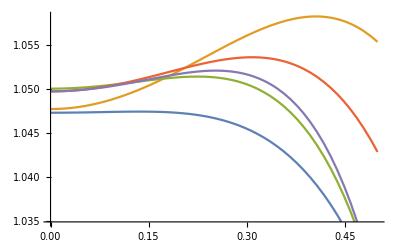

```mathematica
plots=Table[temperatureFullKn0p1[ii][x],{ii,NtensorsFullTheories}];
Plot[plots,{x,0,0.5},PlotLegends->NamesFullTheries]
```

```mathematica
errorFullTheories =Table[ NIntegrate[Abs[ii-θExactKn0p1[x]],{x,-0.5,0.5}],{ii,plots}];
errorFullTheories=Table[Flatten[{NtensorsFullTheories⟦ii⟧,errorFullTheories⟦ii⟧}],{ii,Length[errorFullTheories]}];
```

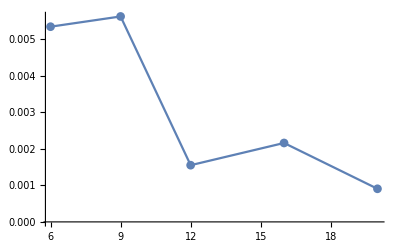

```mathematica
ListPlot[errorFullTheories,Joined->True,PlotMarkers->Automatic]
```

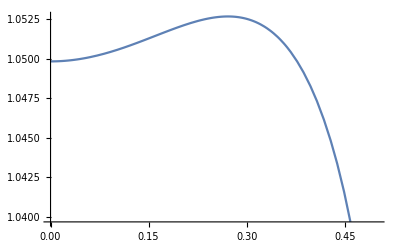

```mathematica
Plot[θExactKn0p1[x],{x,0,0.5},PlotLegends->Automatic]
```

#### Kn 0.3

```mathematica
Kn = 0.3;
θW=1.0;
α=√(2/3);

(*results using MBC*)
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
{temperatureFullKn0p3MBC[ii][x_],stressFullKn0p3MBC[ii][x_],heatFullKn0p3MBC[ii][x_]}=GetHeatConduction[Kn,θW,α,ii,1];,{ii,NtensorsFullTheories}];
```

Num Tensors: 6

Num Tensors: 9

Num Tensors: 12

Num Tensors: 16

Num Tensors: 20

```mathematica
(*results using OBC*)
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
{temperatureFullKn0p3OBC[ii][x_],stressFullKn0p3OBC[ii][x_],heatFullKn0p3OBC[ii][x_]}=GetHeatConduction[Kn,θW,α,ii,0];,{ii,NtensorsFullTheories}];
```

Num Tensors: 6

Num Tensors: 9

Num Tensors: 12

Num Tensors: 16

Num Tensors: 20

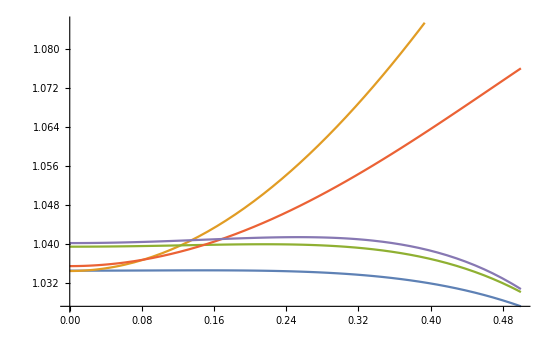

```mathematica
plotMBC=Table[temperatureFullKn0p3MBC[ii][x],{ii,NtensorsFullTheories}];
plotOBC=Table[temperatureFullKn0p3OBC[ii][x],{ii,NtensorsFullTheories}];
Plot[plotOBC,{x,0,0.5},PlotLegends->"AllExpressions"]
```

### Ordered

#### Kn 0.1

```mathematica
Kn = 0.1;
θW=1.0;
α=√(2/3);

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
{temperatureOrdereKn0p1[ii][x_],stressOrdereKn0p1[ii][x_],heatOrdereKn0p1[ii][x_]}=GetHeatConduction[Kn,θW,α,ii,0];,{ii,NtensorsOrderedTheories}];
```

Num Tensors: 8

Num Tensors: 11

Num Tensors: 15

Num Tensors: 19

Num Tensors: 24

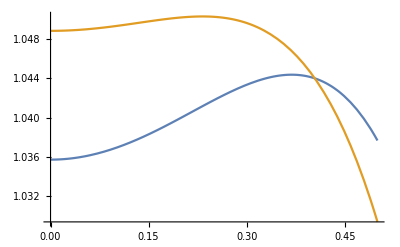

```mathematica
plots=Table[temperatureOrdereKn0p1[ii][x],{ii,NtensorsOrderedTheories}];
Plot[plots,{x,0,0.5}]
```

```mathematica
errorOrderedTheories =Table[ NIntegrate[Abs[ii-θExactKn0p1[x]],{x,-0.5,0.5}],{ii,plots}];
errorOrderedTheories=Table[Flatten[{NtensorsOrderedTheories⟦ii⟧,errorOrderedTheories⟦ii⟧}],{ii,Length[errorOrderedTheories]}];
```

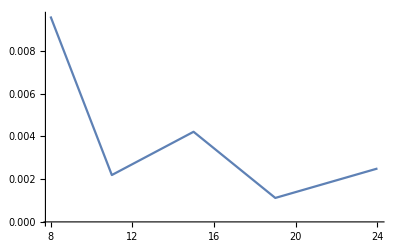

```mathematica
ListPlot[errorOrderedTheories,Joined->True]
```

#### Kn 0.3

```mathematica
Kn = 0.3;
θW=1.0;
α=√(2/3);

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
{temperatureOrderedKn0p3[ii][x_],stressOrderedKn0p3[ii][x_],heatOrderedKn0p3[ii][x_]}=GetHeatConduction[Kn,θW,α,ii];,{ii,NtensorsOrderedTheories}];
```

Num Tensors: 8

Num Tensors: 11

Num Tensors: 15

Num Tensors: 19

Num Tensors: 24

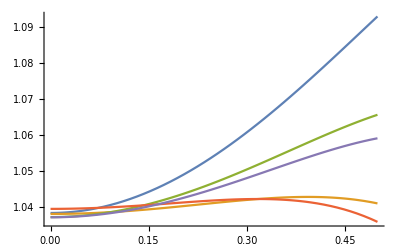

```mathematica
plots=Table[temperatureOrderedKn0p3[ii][x],{ii,NtensorsOrderedTheories}];
Plot[plots,{x,0,0.5}]
```

# Solution for C Code (source independent of Kn)

### G20

```mathematica
OriginalVarKn0p1={-√(3/2)temperatureFullKn0p1[6][x],1/(√2)stressFullKn0p1[6][x]};
OriginalVarKn0p3={-√(3/2)temperatureFullKn0p3[6][x],1/(√2)stressFullKn0p3[6][x]};
precision=15;
N[OriginalVarKn0p1,precision]/.{x->0.60}
N[OriginalVarKn0p3/.{x->0.6},precision]
```

{-1.22478,-0.00705621}

{-1.247,0.000254077}

```mathematica
CForm[OriginalVarKn0p1⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.2829983743239428 + 0.0003362282005094463*cosh(7.453559924999298*y) - 
   0.026127890589687234*pow(y,2) + 0.408248290463863*pow(y,4)

```mathematica
CForm[OriginalVarKn0p1⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(5,0.5)*(-0.0013576450198781716 + 
        0.0004853036051831808*cosh(7.453559924999298*y) - 0.03771236166328255*pow(y,2)
        ))/2.

```mathematica
CForm[OriginalVarKn0p3⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.2898753498434943 + 0.02291602260455048*cosh(2.484519974999766*y) - 
   0.0783836717690617*pow(y,2) + 0.13608276348795437*pow(y,4)

```mathematica
CForm[OriginalVarKn0p3⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(5,0.5)*(-0.03665641553671062 + 0.03307642954873192*cosh(2.484519974999766*y) - 
        0.1131370849898476*pow(y,2)))/2.

### G35

```mathematica
Ntensors=9;
OriginalVarKn0p1={-√(3/2)temperatureFullKn0p1[Ntensors][x],1/(√2)stressFullKn0p1[Ntensors][x]};
OriginalVarKn0p3={-√(3/2)temperatureFullKn0p3[Ntensors][x],1/(√2)stressFullKn0p3[Ntensors][x]};
precision=15;
N[OriginalVarKn0p1,precision]/.{x->0.60}
N[OriginalVarKn0p3/.{x->0.6},precision]
```

{-1.27729,0.00093715}

{-1.40044,0.010108}

```mathematica
CForm[OriginalVarKn0p1⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.2857735434320117 + 0.002601070885430934*cosh(4.662524041201569*y) - 
   0.18289523412781067*pow(y,2) + 0.408248290463863*pow(y,4) + 
   2.168404344971009e-19*sinh(4.662524041201569*y)

```mathematica
CForm[OriginalVarKn0p1⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(5,0.5)*(-0.002715290039756343 + 0.00187716121985606*cosh(4.662524041201569*y) - 
        0.03771236166328255*pow(y,2) - 
        1.0842021724855044e-19*sinh(4.662524041201569*y)))/2.

```mathematica
CForm[OriginalVarKn0p3⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.3660400339849652 + 0.09916339949943631*cosh(1.554174680400523*y) - 
   0.548685702383432*pow(y,2) + 0.13608276348795437*pow(y,4) + 
   6.938893903907228e-18*sinh(1.554174680400523*y)

```mathematica
CForm[OriginalVarKn0p3⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(5,0.5)*(-0.07331283107342124 + 0.07156501924344744*cosh(1.554174680400523*y) - 
        0.1131370849898476*pow(y,2)))/2.

### G45

```mathematica
Ntensors=11;
OriginalVarKn0p1={-√(3/2)temperatureOrdereKn0p1[Ntensors][x],1/(√2)stressOrdereKn0p1[Ntensors][x]};
(*OriginalVarKn0p3={-√(3/2)temperatureOrdereKn0p3[Ntensors][x],1/(√2)stressOrderedKn0p3[Ntensors][x]};*)
(*precision=15;*)
(*N[OriginalVarKn0p1,precision]/.{x->0.60}
N[OriginalVarKn0p3/.{x->0.6},precision]*)
```

```mathematica
CForm[OriginalVarKn0p1⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.2984943215217544 + 0.012487723161170446*cosh(3.84938639795081*y) + 
   0.0014529102471749515*cosh(5.674996469312898*y) + 
   0.000022631203731692907*cosh(10.161219234535377*y) - 0.18289523412781067*pow(y,2) + 
   0.408248290463863*pow(y,4) - 5.421010862427522e-19*sinh(5.674996469312898*y) - 
   3.3881317890172014e-21*sinh(10.161219234535377*y)

-1.2995436998701937 + 0.012092296117067552*cosh(3.849386397950811*y) + 
   0.0015393861867350283*cosh(5.674996469312898*y) + 
   0.000022293298256729303*cosh(10.161219234535377*y) - 
   0.18289523412781067*pow(y,2) + 0.408248290463863*pow(y,4) - 
   8.673617379884035e-19*sinh(3.849386397950811*y) - 
   5.421010862427522e-19*sinh(5.674996469312898*y) - 
   8.470329472543003e-21*sinh(10.161219234535377*y)

```mathematica
CForm[OriginalVarKn0p1⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(5,0.5)*(-0.002715290039756343 + 
        0.0031225329963700333*cosh(3.849386397950811*y) - 
        0.0007338661922650514*cosh(5.674996469312898*y) + 
        0.000033602606211988805*cosh(10.161219234535377*y) - 
        0.03771236166328255*pow(y,2) - 
        1.5178830414797062e-18*sinh(3.849386397950811*y) - 
        1.0842021724855044e-19*sinh(5.674996469312898*y) + 
        1.0164395367051604e-20*sinh(10.161219234535377*y)))/2.

```mathematica
CForm[OriginalVarKn0p3⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.7443580752405021 + 0.39756135791713554*cosh(1.283128799316937*y) + 
   0.07237762337695752*cosh(1.8916654897709662*y) + 
   0.003071248679976172*cosh(3.3870730781784593*y) - 0.548685702383432*pow(y,2) + 
   0.13608276348795437*pow(y,4) - 2.7755575615628914e-17*sinh(1.283128799316937*y) - 
   3.469446951953614e-17*sinh(1.8916654897709662*y) - 
   1.5178830414797062e-18*sinh(3.3870730781784593*y)

```mathematica
CForm[OriginalVarKn0p3⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(5,0.5)*(-0.07331283107342124 + 0.10266027610966066*cosh(1.283128799316937*y) - 
        0.03450433122665434*cosh(1.8916654897709662*y) + 
        0.004629281804058666*cosh(3.3870730781784593*y) - 
        0.1131370849898476*pow(y,2) - 
        4.85722573273506e-17*sinh(1.283128799316937*y) - 
        6.938893903907228e-18*sinh(1.8916654897709662*y) + 
        8.673617379884035e-19*sinh(3.3870730781784593*y)))/2.

### G56

```mathematica
Ntensors=12;
OriginalVarKn0p1={-√(3/2)temperatureFullKn0p1[Ntensors][x],1/(√2)stressFullKn0p1[Ntensors][x],-√(2/5)heatFullKn0p1[Ntensors][x]};
OriginalVarKn0p3={-√(3/2)temperatureFullKn0p3[Ntensors][x],1/(√2)stressFullKn0p3[Ntensors][x],-√(2/5)heatFullKn0p3[Ntensors][x]};
precision=15;
N[OriginalVarKn0p1,precision]/.{x->0.60}
N[OriginalVarKn0p3/.{x->0.6},precision]
```

{-1.20988,0.00956687,-0.0455368}

{-1.24466,0.000780633,-0.0455368}

```mathematica
CForm[OriginalVarKn0p1⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.2991542242917795 + 0.008670378733644997*cosh(3.536982581771994*y) + 
   0.004430725803158755*cosh(5.204696760361044*y) + 
   0.000056930062888828204*cosh(10.45417499077846*y) - 0.18289523412781067*pow(y,2) + 
   0.408248290463863*pow(y,4) - 1.3010426069826053e-18*sinh(5.204696760361044*y) + 
   1.0164395367051604e-20*sinh(10.45417499077846*y)

```mathematica
CForm[OriginalVarKn0p1⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-0.002715290039756343 + 0.0026403019195414515*cosh(3.536982581771994*y) - 
   0.0006407561824316862*cosh(5.204696760361044*y) + 
   0.00008292874116147389*cosh(10.45417499077846*y) - 0.03771236166328255*pow(y,2) - 
   3.469446951953614e-18*sinh(3.536982581771994*y) - 
   3.2526065174565133e-18*sinh(5.204696760361044*y)

```mathematica
CForm[OriginalVarKn0p1⟦3⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(0.4,0.5)*pow(y,3))/3.

```mathematica
CForm[OriginalVarKn0p3⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.7435149236809255 + 0.27723853580237484*cosh(1.178994193923998*y) + 
   0.18476156620816786*cosh(1.734898920120348*y) + 
   0.008511751878547334*cosh(3.4847249969261536*y) - 0.548685702383432*pow(y,2) + 
   0.13608276348795437*pow(y,4) - 5.551115123125783e-17*sinh(1.734898920120348*y) + 
   8.673617379884035e-19*sinh(3.4847249969261536*y)

```mathematica
CForm[OriginalVarKn0p3⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-0.07331283107342124 + 0.0844246209694861*cosh(1.178994193923998*y) - 
   0.02671957622366166*cosh(1.734898920120348*y) + 
   0.0123988773689772*cosh(3.4847249969261536*y) - 0.1131370849898476*pow(y,2) - 
   1.1102230246251565e-16*sinh(1.178994193923998*y) - 
   1.3357370765021415e-16*sinh(1.734898920120348*y)

```mathematica
CForm[OriginalVarKn0p3⟦3⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(0.4,0.5)*pow(y,3))/3.

### G71

```mathematica
Ntensors=15;
OriginalVarKn0p1={-√(3/2)temperatureOrdereKn0p1[Ntensors][x],1/(√2)stressOrdereKn0p1[Ntensors][x],-√(2/5)heatOrdereKn0p1[Ntensors][x]};
OriginalVarKn0p3={-√(3/2)temperatureOrderedKn0p3[Ntensors][x],1/(√2)stressOrderedKn0p3[Ntensors][x],-√(2/5)heatOrderedKn0p3[Ntensors][x]};
precision=15;
N[OriginalVarKn0p1,precision]/.{x->0.60}
N[OriginalVarKn0p3/.{x->0.6},precision]
```

{-1.237,0.00985049,-0.0455368}

{-1.30994,0.00656588,-0.0455368}

```mathematica
CForm[OriginalVarKn0p1⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.3012568770728508 + 0.014368644008044136*cosh(2.9184816217908978*y) + 
   0.000847741867453309*cosh(3.885676724821849*y) + 
   0.0004461674640337943*cosh(5.896124120768356*y) + 
   0.00014238973643247108*cosh(9.591077444821629*y) - 0.18289523412781067*pow(y,2) + 
   0.408248290463863*pow(y,4) + 8.673617379884035e-19*sinh(3.885676724821849*y) - 
   1.3552527156068805e-20*sinh(9.591077444821629*y)

```mathematica
CForm[OriginalVarKn0p1⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-0.002715290039756343 + 0.0018696658823278787*cosh(2.9184816217908978*y) - 
   0.0006185894211626305*cosh(3.885676724821849*y) + 
   0.0004424972314741653*cosh(5.896124120768356*y) + 
   0.00010260159078614521*cosh(9.591077444821629*y) - 0.03771236166328255*pow(y,2) - 
   4.445228907190568e-18*sinh(2.9184816217908978*y) + 
   3.7947076036992655e-19*sinh(3.885676724821849*y) + 
   2.439454888092385e-19*sinh(5.896124120768356*y) - 
   4.0657581468206416e-20*sinh(9.591077444821629*y)

```mathematica
CForm[OriginalVarKn0p1⟦3⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(0.4,0.5)*pow(y,3))/3.

```mathematica
CForm[OriginalVarKn0p3⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.747245655093501 + 0.41369103486028996*cosh(0.9728272072636326*y) + 
   0.02470452567666627*cosh(1.2952255749406163*y) + 
   0.021023428196056175*cosh(1.9653747069227854*y) + 
   0.017552620592354434*cosh(3.197025814940543*y) - 0.548685702383432*pow(y,2) + 
   0.13608276348795437*pow(y,4) + 2.6020852139652106e-17*sinh(1.2952255749406163*y) - 
   1.734723475976807e-18*sinh(3.197025814940543*y)

```mathematica
CForm[OriginalVarKn0p3⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-0.07331283107342124 + 0.053829993510186594*cosh(0.9728272072636326*y) - 
   0.01802666451326118*cosh(1.2952255749406163*y) + 
   0.020850486695610182*cosh(1.9653747069227854*y) + 
   0.012647869434713875*cosh(3.197025814940543*y) - 0.1131370849898476*pow(y,2) - 
   1.249000902703301e-16*sinh(0.9728272072636326*y) + 
   1.214306433183765e-17*sinh(1.2952255749406163*y) + 
   1.214306433183765e-17*sinh(1.9653747069227854*y) - 
   6.071532165918825e-18*sinh(3.197025814940543*y)

```mathematica
CForm[OriginalVarKn0p3⟦3⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(0.4,0.5)*pow(y,3))/3.

### G84

```mathematica
Ntensors=16;
OriginalVarKn0p1={-√(3/2)temperatureFullKn0p1[Ntensors][x],1/(√2)stressFullKn0p1[Ntensors][x],-√(2/5)heatFullKn0p1[Ntensors][x]};
OriginalVarKn0p3={-√(3/2)temperatureFullKn0p3[Ntensors][x],1/(√2)stressFullKn0p3[Ntensors][x],-√(2/5)heatFullKn0p3[Ntensors][x]};
precision=15;
N[OriginalVarKn0p1,precision]/.{x->0.60}
N[OriginalVarKn0p3/.{x->0.6},precision]
```

{-1.25115,0.00072895,-0.0455368}

{-1.33251,-0.00761492,-0.0455368}

```mathematica
CForm[OriginalVarKn0p1⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.3016616131237297 + 0.012498585238508764*cosh(2.867124849692578*y) + 
   0.0026996208249191254*cosh(3.6131625584441966*y) + 
   0.0008429866277644128*cosh(6.002769036811866*y) - 0.18289523412781067*pow(y,2) + 
   0.408248290463863*pow(y,4) - 2.6020852139652106e-18*sinh(2.867124849692578*y) - 
   8.673617379884035e-19*sinh(3.6131625584441966*y) + 
   1.0842021724855044e-19*sinh(6.002769036811866*y)

```mathematica
CForm[OriginalVarKn0p1⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-0.002715290039756343 + 0.0018033048153696892*cosh(2.867124849692578*y) - 
   0.0007033685726265145*cosh(3.6131625584441966*y) + 
   0.0008142812934811178*cosh(6.002769036811866*y) - 0.03771236166328255*pow(y,2) + 
   1.951563910473908e-18*sinh(2.867124849692578*y) - 
   1.6263032587282567e-18*sinh(3.6131625584441966*y) + 
   1.0842021724855044e-19*sinh(6.002769036811866*y)

```mathematica
CForm[OriginalVarKn0p1⟦3⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(0.4,0.5)*pow(y,3))/3.

```mathematica
CForm[OriginalVarKn0p3⟦1⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.7479896311184409 + 0.36064751628260816*cosh(0.9557082832308594*y) + 
   0.07833003503050456*cosh(1.2043875194813989*y) + 
   0.04090384023127845*cosh(2.000923012270622*y) - 0.548685702383432*pow(y,2) + 
   0.13608276348795437*pow(y,4) - 8.326672684688674e-17*sinh(0.9557082832308594*y) - 
   3.469446951953614e-17*sinh(1.2043875194813989*y) + 
   3.469446951953614e-18*sinh(2.000923012270622*y)

```mathematica
CForm[OriginalVarKn0p3⟦2⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-0.07331283107342124 + 0.05203448153153864*cosh(0.9557082832308594*y) - 
   0.0204083789933134*cosh(1.2043875194813989*y) + 
   0.0395109849134863*cosh(2.000923012270622*y) - 0.1131370849898476*pow(y,2) + 
   5.551115123125783e-17*sinh(0.9557082832308594*y) - 
   4.683753385137379e-17*sinh(1.2043875194813989*y) + 
   6.938893903907228e-18*sinh(2.000923012270622*y)

```mathematica
CForm[OriginalVarKn0p3⟦3⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(0.4,0.5)*pow(y,3))/3.

### G105

```mathematica
Ntensors=19;
OriginalVarKn0p1={-√(3/2)temperatureOrdereKn0p1[Ntensors][x],1/(√2)stressOrdereKn0p1[Ntensors][x],-√(2/5)heatOrdereKn0p1[Ntensors][x]};
OriginalVarKn0p3={-√(3/2)temperatureOrderedKn0p3[Ntensors][x],1/(√2)stressOrderedKn0p3[Ntensors][x],-√(2/5)heatOrderedKn0p3[Ntensors][x]};
precision=15;
N[OriginalVarKn0p1,precision]/.{x->0.60}
N[OriginalVarKn0p3/.{x->0.6},precision]
```

{-1.20609,0.00467573,-0.0455368}

{-1.25255,-0.00793698,-0.0455368}

```mathematica
CForm[Chop[OriginalVarKn0p1⟦1⟧]]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.2997563950037463 + 0.009276947895287067*cosh(2.492986999351348*y) + 
   0.00034793324875276896*cosh(3.170853933340145*y) + 
   0.0019572547988298645*cosh(4.388700162109401*y) + 
   0.0017525338749780097*cosh(5.365272100745118*y) + 
   0.0006825478821284116*cosh(7.820516007402679*y) + 
   6.90472273800691e-7*cosh(10.44464164243648*y) + 
   7.880009718028203e-6*cosh(13.163405846932237*y) - 0.18289523412781067*pow(y,2) + 
   0.408248290463863*pow(y,4)

```mathematica
CForm[Chop[OriginalVarKn0p1⟦2⟧]]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-0.002715290039756343 + 0.0008236716794642021*cosh(2.492986999351348*y) - 
   0.00023601868281006479*cosh(3.170853933340145*y) + 
   0.0011001213990571828*cosh(4.388700162109401*y) + 
   0.0006230403314441149*cosh(5.365272100745118*y) - 
   0.00020406994398414134*cosh(7.820516007402679*y) + 
   2.59443373639468e-6*cosh(10.44464164243648*y) + 
   0.000010993753807602042*cosh(13.163405846932237*y) - 0.03771236166328255*pow(y,2)

```mathematica
CForm[OriginalVarKn0p1⟦3⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(0.4,0.5)*pow(y,3))/3.

```mathematica
CForm[Chop[OriginalVarKn0p3⟦1⟧]]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.7441170080467425 + 0.2660463749885166*cosh(0.8309956664504494*y) + 
   0.00981560623079519*cosh(1.0569513111133817*y) + 
   0.07058859198806446*cosh(1.462900054036467*y) + 
   0.07231192665512148*cosh(1.7884240335817059*y) + 
   0.049617730356627546*cosh(2.6068386691342265*y) + 
   0.00009537413540004746*cosh(3.4815472141454937*y) + 
   0.0025738046900230706*cosh(4.387801948977413*y) - 0.548685702383432*pow(y,2) + 
   0.13608276348795437*pow(y,4)

```mathematica
CForm[Chop[OriginalVarKn0p3⟦2⟧]]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-0.07331283107342124 + 0.023621439613073676*cosh(0.8309956664504494*y) - 
   0.006658364677359996*cosh(1.0569513111133817*y) + 
   0.03967598936112579*cosh(1.462900054036467*y) + 
   0.025707489820209463*cosh(1.7884240335817059*y) - 
   0.014834838286982257*cosh(2.6068386691342265*y) + 
   0.0003583661268530281*cosh(3.4815472141454937*y) + 
   0.0035908299765454493*cosh(4.387801948977413*y) - 0.1131370849898476*pow(y,2)

```mathematica
CForm[OriginalVarKn0p3⟦3⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(0.4,0.5)*pow(y,3))/3.

### G120

```mathematica
Ntensors=20;
OriginalVarKn0p1={-√(3/2)temperatureFullKn0p1[Ntensors][x],1/(√2)stressFullKn0p1[Ntensors][x],-√(2/5)heatFullKn0p1[Ntensors][x]};
OriginalVarKn0p3={-√(3/2)temperatureFullKn0p3[Ntensors][x],1/(√2)stressFullKn0p3[Ntensors][x],-√(2/5)heatFullKn0p3[Ntensors][x]};
precision=15;
N[OriginalVarKn0p1,precision]/.{x->0.60}
N[OriginalVarKn0p3/.{x->0.6},precision]
```

{-1.19819,0.0121628,-0.0455368}

{-1.24145,0.00140134,-0.0455368}

```mathematica
CForm[Chop[OriginalVarKn0p1⟦1⟧]]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.2995390567873166 + 0.008828936885305286*cosh(2.480359051432615*y) + 
   0.0008633188573549727*cosh(3.028788951922567*y) + 
   0.003055077322774268*cosh(4.434798678173429*y) + 
   0.0011530952298520565*cosh(7.524303732560254*y) + 
   0.000013607923731562518*cosh(12.976581617858354*y) - 0.18289523412781067*pow(y,2) + 
   0.408248290463863*pow(y,4)

```mathematica
CForm[Chop[OriginalVarKn0p1⟦2⟧]]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-0.002715290039756343 + 0.0008187280616851396*cosh(2.480359051432615*y) - 
   0.0002604386379633425*cosh(3.028788951922567*y) + 
   0.0016721283891165937*cosh(4.434798678173429*y) - 
   0.00017655344915385124*cosh(7.524303732560254*y) + 
   0.00001945869320751019*cosh(12.976581617858354*y) - 0.03771236166328255*pow(y,2)

```mathematica
CForm[OriginalVarKn0p1⟦3⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(0.4,0.5)*pow(y,3))/3.

```mathematica
CForm[Chop[OriginalVarKn0p3⟦1⟧]]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-1.7436949415826675 + 0.2523069701617391*cosh(0.8267863504775383*y) + 
   0.02533033765112578*cosh(1.0095963173075224*y) + 
   0.11056926376618245*cosh(1.4782662260578097*y) + 
   0.07739730163732568*cosh(2.508101244186751*y) + 
   0.004179811421577409*cosh(4.325527205952785*y) - 0.548685702383432*pow(y,2) + 
   0.13608276348795437*pow(y,4)

```mathematica
CForm[Chop[OriginalVarKn0p3⟦2⟧]]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-0.07331283107342124 + 0.02339701815900208*cosh(0.8267863504775383*y) - 
   0.007641439290718827*cosh(1.0095963173075224*y) + 
   0.060517618827160266*cosh(1.4782662260578097*y) - 
   0.011850504802646761*cosh(2.508101244186751*y) + 
   0.005976934448057989*cosh(4.325527205952785*y) - 0.1131370849898476*pow(y,2)

```mathematica
CForm[OriginalVarKn0p3⟦3⟧]/.{Power->pow,Sqrt->sqrt,Cosh->cosh,Sinh->sinh,x->y}
```

-(pow(0.4,0.5)*pow(y,3))/3.